```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
Print["Runs in the list: ",runNum={11159,11166,11208,11239,11277,11305,11357,11363,11409,11412,11445,11448}];(*{010119,10124,10135,10166,10189,10191,10207,10246,10270,10273,10281,10345,10386,10391,10417,10420,10463,10471,10497,10541}*)
Print["#Runs in the list: ",runn=Dimensions[runNum][[1]]];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
histbeg=100;histlast=1400;ChNum=1;
chnum={1,2,3,4,5,6,7,8,9,11,12,13,14,15,16,17,18,19};
steps={28,2,2,2,2,20,160,2,2,64,1};(**)
Print["Number of Steps: ",Dimensions[steps][[1]]];
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

Runs in the list: {11159,11166,11208,11239,11277,11305,11357,11363,11409,11412,11445,11448}

#Runs in the list: 12

Number of Steps: 11

```mathematica
bkgcou=Table[0,{k,1,runn}];moncou=Table[0,{k,1,runn}];
Monitor[Quiet[
icycle=0;
histbeg2=0*(10^9);histlast2=300*(10^9);binw2=1*(10^9);
For[runi=1,runi≤1(*runn*),runi++,
Clear[data,histdata2];
ptdat2=Table[Table[{0,{0,0}},{k,1,Round[(histlast2-histbeg2)/binw2]}],{l,1,runn}];
maxCy=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_Meta3.edm"],metaStructure2][[-1]][[2]];
bkgcou[[runi]]={};
moncou[[runi]]={};
For[icycle=1,icycle≤maxCy,icycle++,
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_UCNdet_",IntegerString[icycle,10,3],"_0001.fast.ascii"],metaStructure];
dimdata=Dimensions[data][[1]];
histdata2=HistogramList[data[[1;;dimdata,4]],{histbeg2,histlast2,binw2}];
For[i=1,i<=Dimensions[histdata2[[2]]][[1]],i++,
ptdat2[[icycle]][[i]][[1]]=(histdata2[[1]][[i]]+((-histdata2[[1]][[1]]+histdata2[[1]][[2]])/2))/(10^9);
ptdat2[[icycle]][[i]][[2]][[1]]=histdata2[[2]][[i]];
ptdat2[[icycle]][[i]][[2]][[2]]=Sqrt[ptdat2[[icycle]][[i]][[2]][[1]]];
bkgcou[[runi]]=
AppendTo[bkgcou[[runi]],Abs[Total[ptdat2[[icycle]][[;;,2]][[;;,1]][[218-66;;218]]]-Floor[Mean[ptdat2[[icycle]][[;;,2]][[;;,1]][[218-99;;218]]]*67]]];
moncou[[runi]]=
AppendTo[moncou[[runi]],N[Mean[ptdat2[[icycle]][[;;,2]][[;;,1]][[218-99;;218]]]]];
];
];
];
];,
ProgressIndicator[icycle/maxCy,ImageSize->{1000,100}]]
ProgressIndicator[1,ImageSize->{1000,100}]
```

Table::iterb: Iterator {k, 1, runn} does not have appropriate bounds.

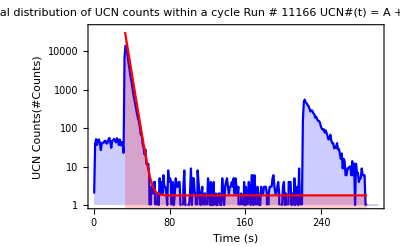

```mathematica
Clear[nlm]
ftdat=Table[Transpose[{ptdat2[[1]][[;;,1]],ptdat2[[2]][[;;,2]][[;;,1]]}][[k]],{k,35,217}];
nlm=NonlinearModelFit[ftdat,{aa+(bb Exp[cc (xx-dd)])},{{aa,1},{bb,30000},{cc,-.3},{dd,33}},xx,Method->NMinimize];
fitparam={aa/.nlm[[1]][[2]],bb/.nlm[[1]][[2]],cc/.nlm[[1]][[2]],dd/.nlm[[1]][[2]]};
fitparamerr=SetPrecision[N[nlm["ParameterErrors"]],10];
Show[EDALogListPlot[ptdat2[[1]]+.01, PlotStyle->{Blue},Joined->True,Filling->Axis,PlotRange->{{0,300},{1,40000}},Frame->True,PlotRange->Full,FrameLabel->{"Time (s)","UCN Counts(#Counts)"},LabelStyle->{Black,18},TicksStyle->Directive[FontSize->40],PlotLabel->StringJoin["Typical temporal distribution of UCN counts within a cycle \n Run # 11166 \n UCN#(t) = A + Bⅇ^(-C (t - D)), tϵ(32,218)"],ImageSize->{1000}],
EDALogListPlot[Table[{k,1.8+32000Exp[-.345(k-33)]},{k,33,288}], PlotStyle->{Red},Joined->True,Filling->Axis,PlotRange->{{0,300},{.1,40000}},Frame->True,PlotRange->Full,FrameLabel->{"Time (s)","UCN Counts(#Counts)"},LabelStyle->{Black,18},TicksStyle->Directive[FontSize->40],ImageSize->{1000}]]
(*ListLogPlot[{Transpose[{ptdat2[[2]][[;;,1]],ptdat2[[2]][[;;,2]][[;;,1]]}],Table[{k,fitparam[[1]]+fitparam[[2]]Exp[fitparam[[3]](k-fitparam[[4]])]},{k,33,218}]},PlotStyle->{Blue,Red,Gray},Joined->True,Filling->Axis,PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"Time (s)","Normalized Counts(#Counts)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},PlotLegends->ToString[runNum[[runi-1]]],ImageSize->{1000}]*)
```

```mathematica
bkgcouu={};moncouu={};
bkgcoud={};moncoud={};
(*ptdat2=Table[{0,0},{k,1,Round[(histlast2-histbeg2)/binw2]}];
Interval: ptdat2[[icycle]][[i]][[1]]=(histdata2[[1]][[i]]+((-histdata2[[1]][[1]]+histdata2[[1]][[2]])/2))/(10^9);*)
histbeg2=0*(10^9);histlast2=300*(10^9);binw2=1*(10^9);
runnum=runNum[[1]];
Monitor[
Quiet[
Print[DateObject[Now]];
icycle=0;
Clear[data,histdata2];
maxCy=ReadList[StringJoin[AscDir,"\\",IntegerString[runnum,10,6],"\\",IntegerString[runnum,10,6],"_Meta3.edm"],metaStructure2][[-1]][[2]];
For[icycle=1,icycle≤maxCy,icycle++,
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runnum,10,6],"\\",IntegerString[runnum,10,6],"_UCNdet_",IntegerString[icycle,10,3],"_0001.fast.ascii"],metaStructure];
(**)
datau=Select[data,#[[3]]<10&];
dimdata=Dimensions[datau][[1]];
histdata2=HistogramList[datau[[1;;dimdata,4]],{histbeg2,histlast2,binw2}];
bkgcouu=AppendTo[bkgcouu,N[Abs[Total[histdata2[[2]][[218-66;;218]]]-Floor[Mean[histdata2[[2]][[218-99;;218]]]*67]]]];
moncouu=AppendTo[moncouu,N[Mean[histdata2[[2]][[218-99;;218]]]]];
(**)
datad=Select[data,#[[3]]>10&];
dimdata=Dimensions[datad][[1]];
histdata2=HistogramList[datad[[1;;dimdata,4]],{histbeg2,histlast2,binw2}];
bkgcoud=AppendTo[bkgcoud,N[Abs[Total[histdata2[[2]][[218-66;;218]]]-Floor[Mean[histdata2[[2]][[218-99;;218]]]*67]]]];
moncoud=AppendTo[moncoud,N[Mean[histdata2[[2]][[218-99;;218]]]]];
];
Print[DateObject[Now]];
];,
ProgressIndicator[icycle/maxCy,ImageSize->{1000,100}]
];
ProgressIndicator[1,ImageSize->{1000,100}]
```

Tue 6 Dec 2016 12:22:15GMT+1.

Tue 6 Dec 2016 12:50:30GMT+1.

```mathematica
info=ReadList[StringJoin[AscDir,"\\",IntegerString[runnum,10,6],"\\",IntegerString[runnum,10,6],"_Meta3.edm"],metaStructure2];
(*6->HV, SF1->25, SF2->26, RF->-1*)
```

```mathematica
pu01={};mu01={};
pd01={};md01={};
pu11={};mu11={};
pd11={};md11={};
pu02={};mu02={};
pd02={};md02={};
pu12={};mu12={};
pd12={};md12={};
nu[rff_]=10000(1+.8Cos[((rff-30.231)*2Pi)/(180*0.00004)]);
nd[rff_]=10000(1-.8Cos[((rff-30.231)*2Pi)/(180*0.00004)]);
For[i=1,i≤Dimensions[info][[1]],i++,
If[((info[[i]][[6]]>10)&&(info[[i]][[25]]==0)&&(info[[i]][[26]]==1)),
pu01=AppendTo[pu01,{info[[i]][[-1]],bkgcouu[[i]]+nu[info[[i]][[-1]]]}];
pd01=AppendTo[pd01,{info[[i]][[-1]],bkgcoud[[i]]+nd[info[[i]][[-1]]]}];
];
If[((info[[i]][[6]]<-10)&&(info[[i]][[25]]==0)&&(info[[i]][[26]]==1)),
mu01=AppendTo[mu01,{info[[i]][[-1]],bkgcouu[[i]]+nu[info[[i]][[-1]]]}];
md01=AppendTo[md01,{info[[i]][[-1]],bkgcoud[[i]]+nd[info[[i]][[-1]]]}];
];
If[((info[[i]][[6]]>10)&&(info[[i]][[25]]==1)&&(info[[i]][[26]]==1)),
pu11=AppendTo[pu11,{info[[i]][[-1]],bkgcouu[[i]]+nu[info[[i]][[-1]]]}];
pd11=AppendTo[pd11,{info[[i]][[-1]],bkgcoud[[i]]+nd[info[[i]][[-1]]]}];
];
If[((info[[i]][[6]]<-10)&&(info[[i]][[25]]==1)&&(info[[i]][[26]]==1)),
mu11=AppendTo[mu11,{info[[i]][[-1]],bkgcouu[[i]]+nu[info[[i]][[-1]]]}];
md11=AppendTo[md11,{info[[i]][[-1]],bkgcoud[[i]]+nd[info[[i]][[-1]]]}];
];
(**)
If[((info[[i]][[6]]>10)&&(info[[i]][[25]]==0)&&(info[[i]][[26]]==2)),
pu02=AppendTo[pu02,{info[[i]][[-1]],bkgcouu[[i]]+nu[info[[i]][[-1]]]}];
pd02=AppendTo[pd02,{info[[i]][[-1]],bkgcoud[[i]]+nd[info[[i]][[-1]]]}];
];
If[((info[[i]][[6]]<-10)&&(info[[i]][[25]]==0)&&(info[[i]][[26]]==2)),
mu02=AppendTo[mu02,{info[[i]][[-1]],bkgcouu[[i]]+nu[info[[i]][[-1]]]}];
md02=AppendTo[md02,{info[[i]][[-1]],bkgcoud[[i]]+nd[info[[i]][[-1]]]}];
];
If[((info[[i]][[6]]>10)&&(info[[i]][[25]]==1)&&(info[[i]][[26]]==2)),
pu12=AppendTo[pu12,{info[[i]][[-1]],bkgcouu[[i]]+nu[info[[i]][[-1]]]}];
pd12=AppendTo[pd12,{info[[i]][[-1]],bkgcoud[[i]]+nd[info[[i]][[-1]]]}];
];
If[((info[[i]][[6]]<-10)&&(info[[i]][[25]]==1)&&(info[[i]][[26]]==2)),
mu12=AppendTo[mu12,{info[[i]][[-1]],bkgcouu[[i]]+nu[info[[i]][[-1]]]}];
md12=AppendTo[md12,{info[[i]][[-1]],bkgcoud[[i]]+nd[info[[i]][[-1]]]}];
];
];
```

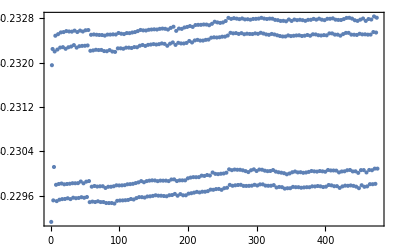

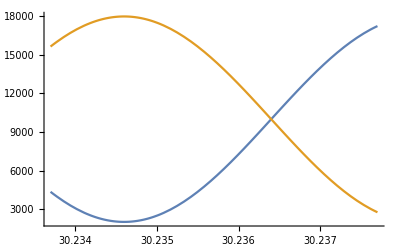

```mathematica
ListPlot[info[[;;,-1]],PlotRange->Full,Frame->True]
Plot[{nu[x],nd[x]},{x,30.2337,30.2377},PlotRange->Full]
```

```mathematica
Quiet[Needs["PhysicalConstants`"]];
ee=ElectronCharge/Coulomb;
hp=PlanckConstant/(2 π Joule Second);
eEf=11200;
cm=0.01;
fitp[ftdata_]:=(
nlm=NonlinearModelFit[ftdata,(aa(1+bb Cos[((xx-cc)*2Pi)/(180*0.00004)])),{{aa,10000},{bb,.8},{cc,30.231}},xx];
Return[{{aa/.nlm[[1]][[2]],nlm["ParameterErrors"][[1]]},{bb/.nlm[[1]][[2]],nlm["ParameterErrors"][[2]]},{cc/.nlm[[1]][[2]],nlm["ParameterErrors"][[3]]}}];
);
fitm[ftdata_]:=(
nlm=NonlinearModelFit[ftdata,(aa(1-bb Cos[((xx-cc)*2Pi)/(180*0.00004)])),{{aa,10000},{bb,.8},{cc,30.231}},xx];
Return[{{aa/.nlm[[1]][[2]],nlm["ParameterErrors"][[1]]},{bb/.nlm[[1]][[2]],nlm["ParameterErrors"][[2]]},{cc/.nlm[[1]][[2]],nlm["ParameterErrors"][[3]]}}];
);
Print["{NANOSc(A,B),SF1(0,1),SF2(1,2)}"];
Print["{A,0,1}:(e.cm) = ",a01=Abs[(hp cm SubtractWithError[fitp[pu01][[3]],fitm[mu01][[3]]]Sqrt[Total[pu01[[;;,2]]]])/(4(ee eEf)Sqrt[10000])]];
Print["{B,0,1}:(e.cm) = ",b01=Abs[(hp cm SubtractWithError[fitp[pd01][[3]],fitm[md01][[3]]]Sqrt[Total[pd01[[;;,2]]]])/(4(ee eEf)  Sqrt[10000])]];
Print["{A,1,1}:(e.cm) = ",a11=Abs[(hp cm SubtractWithError[fitp[pu11][[3]],fitm[mu11][[3]]]Sqrt[Total[pu11[[;;,2]]]])/(4(ee eEf) Sqrt[10000])]];
Print["{B,1,1}:(e.cm) = ",b11=Abs[(hp cm SubtractWithError[fitp[pd11][[3]],fitm[md11][[3]]] Sqrt[Total[pd11[[;;,2]]]])/(4(ee eEf)Sqrt[10000])]];
Print["{A,0,2}:(e.cm) = ",a02=Abs[(hp cm SubtractWithError[fitp[pu02][[3]],fitm[mu02][[3]]]Sqrt[Total[pu02[[;;,2]]]])/(4(ee eEf)Sqrt[10000])]];
Print["{B,0,2}:(e.cm) = ",b02=Abs[(hp cm SubtractWithError[fitp[pd02][[3]],fitm[md02][[3]]]Sqrt[Total[pd02[[;;,2]]]])/(4(ee eEf) Sqrt[10000])]];
Print["{A,1,2}:(e.cm) = ",a12=Abs[(hp cm SubtractWithError[fitp[pu12][[3]],fitm[mu12][[3]]]Sqrt[Total[pu12[[;;,2]]]])/(4(ee eEf)Sqrt[10000])]];
Print["{B,1,2}:(e.cm) = ",b12=Abs[(hp cm SubtractWithError[fitp[pd12][[3]],fitm[md12][[3]]]Sqrt[Total[pd12[[;;,2]]]])/(4(ee eEf)Sqrt[10000])]];
Print["Cumulative:(e.cm) = ",1/√((1/a01[[2]])^2+(1/b01[[2]])^2+(1/a11[[2]])^2+(1/b11[[2]])^2+(1/a02[[2]])^2+(1/b02[[2]])^2+(1/a12[[2]])^2+(1/b12[[2]]))];
```

{NANOSc(A,B),SF1(0,1),SF2(1,2)}

{A,0,1}:(e.cm) = {4.81876×10^-28,5.52394×10^-28}

{B,0,1}:(e.cm) = {1.97201×10^-28,6.70483×10^-28}

{A,1,1}:(e.cm) = {8.18265×10^-29,6.8968×10^-28}

{B,1,1}:(e.cm) = {1.67688×10^-27,6.73393×10^-28}

{A,0,2}:(e.cm) = {4.4635×10^-28,5.28573×10^-28}

{B,0,2}:(e.cm) = {1.31527×10^-29,5.78718×10^-28}

{A,1,2}:(e.cm) = {1.74909×10^-28,6.41331×10^-28}

{B,1,2}:(e.cm) = {6.61489×10^-28,7.01179×10^-28}

Cumulative:(e.cm) = 2.30598×10^-28

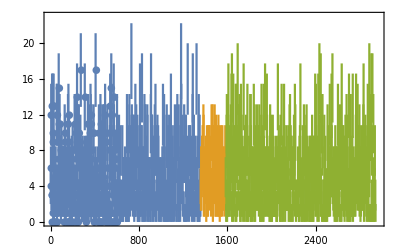

```mathematica
EDAListPlot[
Table[{2k,{bkgcouu[[k]],Sqrt[bkgcouu[[k]]]}},{k,1,Dimensions[bkgcouu][[1]]}],Table[{2(k+Dimensions[bkgcouu][[1]]),{Round[(bkgcoud[[k]]+bkgcouu[[k]])/2],Sqrt[Round[(bkgcoud[[k]]+bkgcouu[[k]])/2]]}},{k,1,Dimensions[bkgcoud][[1]]/6}],
Table[{2(k+Dimensions[bkgcouu][[1]]/6+Dimensions[bkgcoud][[1]]),{bkgcoud[[k]],Sqrt[bkgcoud[[k]]]}},{k,1,Dimensions[bkgcoud][[1]]}],
Frame->True,FrameLabel->{"Cycle (#)","UCN Counts (#)"},PlotMarkers->{Automatic,10},TicksStyle->Directive[FontSize->40],LabelStyle->{Black,18},PlotLegends->{"HV+","HV0","HV-"},PlotLabel->"Background Counts acquired during an nEDM run",ImageSize->{1000},PlotRange->{{0,2960},{0,23}}
]
```

```mathematica
(*
pu01={};mu01={};
pd01={};md01={};
pu11={};mu11={};
pd11={};md11={};
pu02={};mu02={};
pd02={};md02={};
pu12={};mu12={};
pd12={};md12={};
*)
```

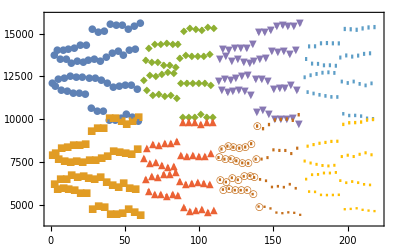

```mathematica
(*Jut for myself*)
EDAListPlot[Table[{k,{pu01[[k]][[2]],Sqrt[pu01[[k]][[2]]]}},{k,1,Dimensions[pu01][[1]]}],
Table[{k,{pd01[[k]][[2]],Sqrt[pd01[[k]][[2]]]}},{k,1,Dimensions[pd01][[1]]}],
Table[{k+2+Dimensions[pd01][[1]],{pu11[[k]][[2]],Sqrt[pu11[[k]][[2]]]}},{k,1,Dimensions[pu11][[1]]}],
Table[{k+2+Dimensions[pd01][[1]],{pd11[[k]][[2]],Sqrt[pd11[[k]][[2]]]}},{k,1,Dimensions[pd11][[1]]}],
Table[{k+4+Dimensions[pd01][[1]]+Dimensions[pd11][[1]],{pu02[[k]][[2]],Sqrt[pu02[[k]][[2]]]}},{k,1,Dimensions[pu02][[1]]}],
Table[{k+4+Dimensions[pd01][[1]]+Dimensions[pd11][[1]],{pd02[[k]][[2]],Sqrt[pd02[[k]][[2]]]}},{k,1,Dimensions[pd02][[1]]}],
Table[{k+6+Dimensions[pd01][[1]]+Dimensions[pd11][[1]]+Dimensions[pd02][[1]],{pu12[[k]][[2]],Sqrt[pu12[[k]][[2]]]}},{k,1,Dimensions[pu12][[1]]}],
Table[{k+6+Dimensions[pd01][[1]]+Dimensions[pd11][[1]]+Dimensions[pd02][[1]],{pd12[[k]][[2]],Sqrt[pd12[[k]][[2]]]}},{k,1,Dimensions[pd12][[1]]}],
Frame->True,FrameLabel->{"Cycle (#)","UCN Counts (#)"},PlotMarkers->{Automatic,10},TicksStyle->Directive[FontSize->40],LabelStyle->{Black,18},PlotLegends->{"HV+","HV0","HV-"},PlotLabel->"Background Counts acquired during an +HV nEDM run",ImageSize->{1000},PlotRange->{{0,220},{4000,16000}}
]
```

```mathematica
HistogramList[bkgcouu][[2]]
```

{56,107,86,84,65,55,50,42,30,29,26,18,11,5,4,5,2,2,2}

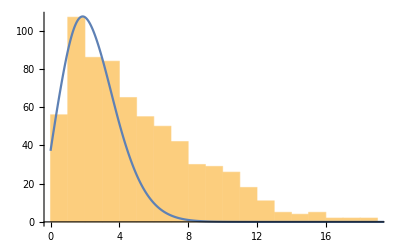

```mathematica
Show[Histogram[bkgcouu],ListLinePlot[Table[{x,(Max[HistogramList[bkgcouu][[2]]]/PDF[PoissonDistribution[2.4],2])PDF[PoissonDistribution[2.4],x]},{x,0,20}],InterpolationOrder->3,PlotRange->{{0,20},{0,300}}]]
```

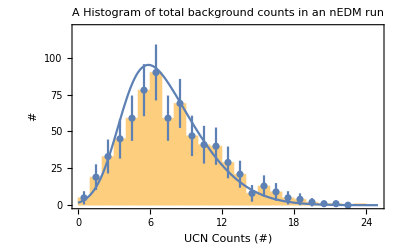

```mathematica
bkgt=Table[(bkgcouu[[k]]+Round[5.5RandomReal[]]),{k,1,Dimensions[bkgcouu][[1]]}];
Show[{
Histogram[bkgt,25,Frame->True,FrameLabel->{"UCN Counts (#)","#"},TicksStyle->Directive[FontSize->40],PlotLabel->"A Histogram of total background counts in an nEDM run",LabelStyle->{Black,18},ImageSize->{1000},PlotRange->{{0,25},{0,120}}],
Plot[(Max[HistogramList[bkgt,25][[2]]]/PDF[SkewNormalDistribution[3.5,5,3],5])PDF[SkewNormalDistribution[3.5,5,3],x],{x,0,25},Frame->True,FrameLabel->{"UCN Counts (#)","#"},TicksStyle->Directive[FontSize->40],PlotLabel->"A Histogram of total background counts in an nEDM run",LabelStyle->{Black,18},ImageSize->{1000},PlotRange->{{0,25},{0,120}}],EDAListPlot[Table[{(k-.5),Transpose[{HistogramList[bkgt,25][[2]],2Sqrt[HistogramList[bkgt,25][[2]]]}][[k]]},{k,1,23}],Frame->True,FrameLabel->{"UCN Counts (#)","#"},TicksStyle->Directive[FontSize->40],PlotLabel->"A Histogram of total background counts in an nEDM run",LabelStyle->{Black,18},ImageSize->{1000},PlotRange->{{0,25},{0,120}}]
}]
```

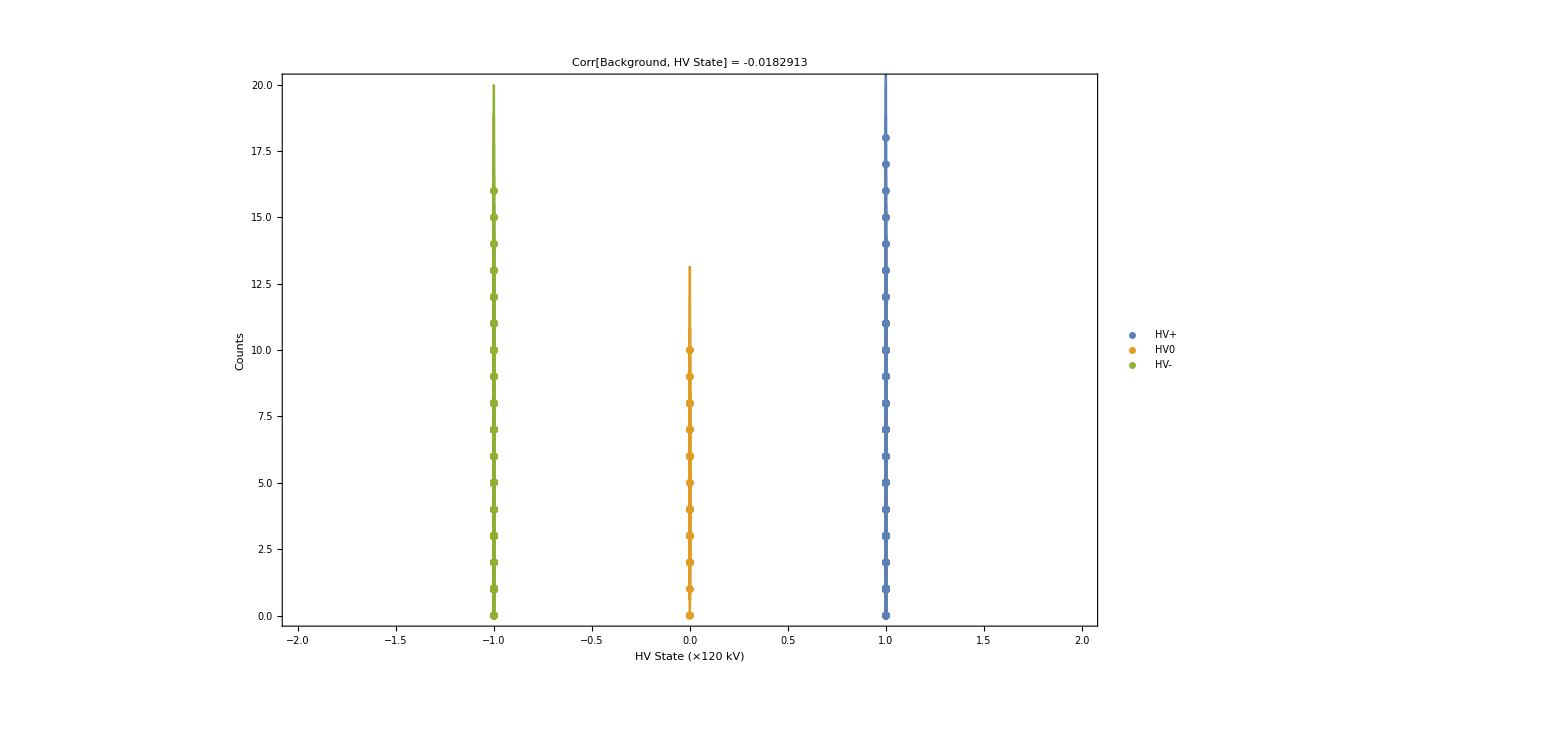

```mathematica
(*pu01={};mu01={};
pd01={};md01={};
pu11={};mu11={};
pd11={};md11={};
pu02={};mu02={};
pd02={};md02={};
pu12={};mu12={};
pd12={};md12={};*)
corrbkg=Correlation[Join[Table[{bkgcouu[[k]],1},{k,1,Dimensions[bkgcouu][[1]]}],
Table[{Round[(bkgcoud[[k]]+bkgcouu[[k]])/2],0},{k,1,Dimensions[bkgcoud][[1]]/6}],
Table[{bkgcoud[[k]],-1},{k,1,Dimensions[bkgcoud][[1]]}]]][[1]][[2]];
EDAListPlot[Table[{1,{bkgcouu[[k]],Sqrt[bkgcouu[[k]]]}},{k,1,Dimensions[bkgcouu][[1]]}],
Table[{0,{Round[(bkgcoud[[k]]+bkgcouu[[k]])/2],Sqrt[Round[(bkgcoud[[k]]+bkgcouu[[k]])/2]]}},{k,1,Dimensions[bkgcoud][[1]]/6}],
Table[{-1,{bkgcoud[[k]],Sqrt[bkgcoud[[k]]]}},{k,1,Dimensions[bkgcoud][[1]]}],
Frame->True,FrameLabel->{Style["HV State (×120 kV)",FontSize->18],Style["Counts",FontSize->18]},TicksStyle->Large,PlotLabel->Style[StringJoin["Corr[Background, HV State] = ",ToString[corrbkg]],FontSize->18],LabelStyle->{18},PlotRange->{{-2,2},{0,20}},PlotLegends->{"HV+","HV0","HV-"},ImageSize->1200]
```

```mathematica
pu01={};mu01={};
pd01={};md01={};
pu11={};mu11={};
pd11={};md11={};
pu02={};mu02={};
pd02={};md02={};
pu12={};mu12={};
pd12={};md12={};
For[i=1,i≤Dimensions[info][[1]],i++,
If[((info[[i]][[6]]>10)&&(info[[i]][[25]]==0)&&(info[[i]][[26]]==1)),
pu01=AppendTo[pu01,{info[[i]][[-1]],bkgcouu[[i]]}];
pd01=AppendTo[pd01,{info[[i]][[-1]],bkgcoud[[i]]}];
];
If[((info[[i]][[6]]<-10)&&(info[[i]][[25]]==0)&&(info[[i]][[26]]==1)),
mu01=AppendTo[mu01,{info[[i]][[-1]],bkgcouu[[i]]}];
md01=AppendTo[md01,{info[[i]][[-1]],bkgcoud[[i]]}];
];
If[((info[[i]][[6]]>10)&&(info[[i]][[25]]==1)&&(info[[i]][[26]]==1)),
pu11=AppendTo[pu11,{info[[i]][[-1]],bkgcouu[[i]]}];
pd11=AppendTo[pd11,{info[[i]][[-1]],bkgcoud[[i]]}];
];
If[((info[[i]][[6]]<-10)&&(info[[i]][[25]]==1)&&(info[[i]][[26]]==1)),
mu11=AppendTo[mu11,{info[[i]][[-1]],bkgcouu[[i]]}];
md11=AppendTo[md11,{info[[i]][[-1]],bkgcoud[[i]]}];
];
(**)
If[((info[[i]][[6]]>10)&&(info[[i]][[25]]==0)&&(info[[i]][[26]]==2)),
pu02=AppendTo[pu02,{info[[i]][[-1]],bkgcouu[[i]]}];
pd02=AppendTo[pd02,{info[[i]][[-1]],bkgcoud[[i]]}];
];
If[((info[[i]][[6]]<-10)&&(info[[i]][[25]]==0)&&(info[[i]][[26]]==2)),
mu02=AppendTo[mu02,{info[[i]][[-1]],bkgcouu[[i]]}];
md02=AppendTo[md02,{info[[i]][[-1]],bkgcoud[[i]]}];
];
If[((info[[i]][[6]]>10)&&(info[[i]][[25]]==1)&&(info[[i]][[26]]==2)),
pu12=AppendTo[pu12,{info[[i]][[-1]],bkgcouu[[i]]}];
pd12=AppendTo[pd12,{info[[i]][[-1]],bkgcoud[[i]]}];
];
If[((info[[i]][[6]]<-10)&&(info[[i]][[25]]==1)&&(info[[i]][[26]]==2)),
mu12=AppendTo[mu12,{info[[i]][[-1]],bkgcouu[[i]]}];
md12=AppendTo[md12,{info[[i]][[-1]],bkgcoud[[i]]}];
];
];
```

```mathematica
nu[rff_]=10000(1+.8Cos[((rff-30.231)*2Pi)/(180*0.00004)]);
nd[rff_]=10000(1-.8Cos[((rff-30.231)*2Pi)/(180*0.00004)]);
For[i=1,i≤Dimensions[info][[1]],i++,
If[((info[[i]][[6]]>10)&&(info[[i]][[25]]==0)&&(info[[i]][[26]]==1)),
pu01=AppendTo[pu01,{info[[i]][[-1]],bkgcouu[[i]]+nd[info[[i]][[-1]]]}];
pd01=AppendTo[pd01,{info[[i]][[-1]],bkgcoud[[i]]+nu[info[[i]][[-1]]]}];
];
If[((info[[i]][[6]]<-10)&&(info[[i]][[25]]==0)&&(info[[i]][[26]]==1)),
mu01=AppendTo[mu01,{info[[i]][[-1]],bkgcouu[[i]]+nd[info[[i]][[-1]]]}];
md01=AppendTo[md01,{info[[i]][[-1]],bkgcoud[[i]]+nu[info[[i]][[-1]]]}];
];
If[((info[[i]][[6]]>10)&&(info[[i]][[25]]==1)&&(info[[i]][[26]]==1)),
pu11=AppendTo[pu11,{info[[i]][[-1]],bkgcoud[[i]]+nd[info[[i]][[-1]]]}];
pd11=AppendTo[pd11,{info[[i]][[-1]],bkgcouu[[i]]+nu[info[[i]][[-1]]]}];
];
If[((info[[i]][[6]]<-10)&&(info[[i]][[25]]==1)&&(info[[i]][[26]]==1)),
mu11=AppendTo[mu11,{info[[i]][[-1]],bkgcoud[[i]]+nd[info[[i]][[-1]]]}];
md11=AppendTo[md11,{info[[i]][[-1]],bkgcouu[[i]]+nu[info[[i]][[-1]]]}];
];
(**)
If[((info[[i]][[6]]>10)&&(info[[i]][[25]]==0)&&(info[[i]][[26]]==2)),
pu02=AppendTo[pu02,{info[[i]][[-1]],bkgcouu[[i]]+nd[info[[i]][[-1]]]}];
pd02=AppendTo[pd02,{info[[i]][[-1]],bkgcoud[[i]]+nu[info[[i]][[-1]]]}];
];
If[((info[[i]][[6]]<-10)&&(info[[i]][[25]]==0)&&(info[[i]][[26]]==2)),
mu02=AppendTo[mu02,{info[[i]][[-1]],bkgcouu[[i]]+nd[info[[i]][[-1]]]}];
md02=AppendTo[md02,{info[[i]][[-1]],bkgcoud[[i]]+nu[info[[i]][[-1]]]}];
];
If[((info[[i]][[6]]>10)&&(info[[i]][[25]]==1)&&(info[[i]][[26]]==2)),
pu12=AppendTo[pu12,{info[[i]][[-1]],bkgcoud[[i]]+nd[info[[i]][[-1]]]}];
pd12=AppendTo[pd12,{info[[i]][[-1]],bkgcouu[[i]]+nu[info[[i]][[-1]]]}];
];
If[((info[[i]][[6]]<-10)&&(info[[i]][[25]]==1)&&(info[[i]][[26]]==2)),
mu12=AppendTo[mu12,{info[[i]][[-1]],bkgcoud[[i]]+nd[info[[i]][[-1]]]}];
md12=AppendTo[md12,{info[[i]][[-1]],bkgcouu[[i]]+nu[info[[i]][[-1]]]}];
];
];
```

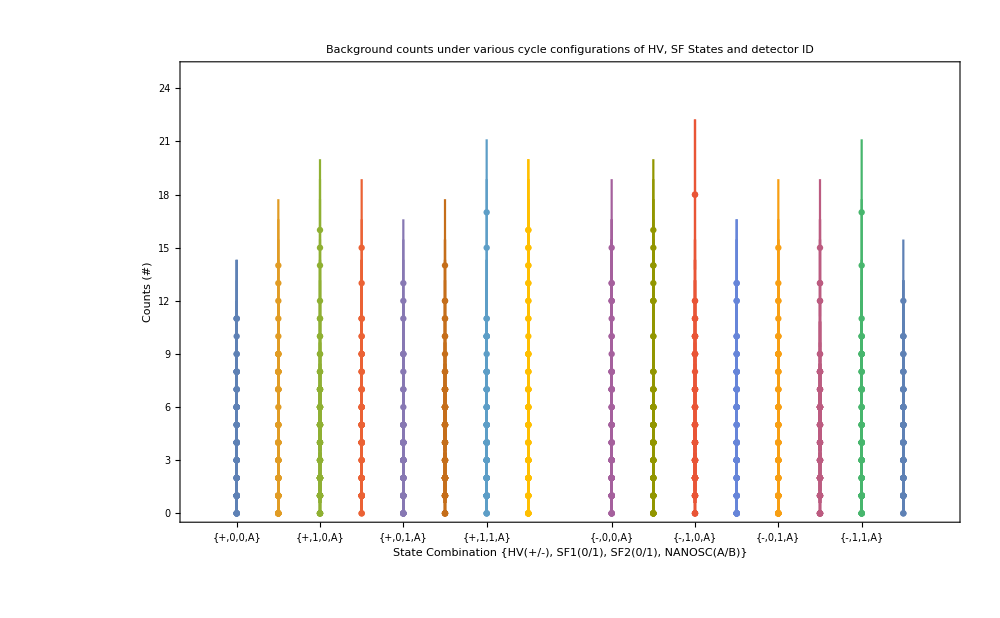

```mathematica
EDAListPlot[Table[{{-8},{pu01[[;;,2]][[k]],Sqrt[pu01[[;;,2]][[k]]]}},{k,1,Dimensions[pu01[[;;,2]]][[1]]}],
Table[{-7,{pd01[[;;,2]][[k]],Sqrt[pd01[[;;,2]][[k]]]}},{k,1,Dimensions[pd01[[;;,2]]][[1]]}],
Table[{-6,{pu11[[;;,2]][[k]],Sqrt[pu11[[;;,2]][[k]]]}},{k,1,Dimensions[pu11[[;;,2]]][[1]]}],
Table[{-5,{pd11[[;;,2]][[k]],Sqrt[pd11[[;;,2]][[k]]]}},{k,1,Dimensions[pd11[[;;,2]]][[1]]}],
Table[{-4,{pu02[[;;,2]][[k]],Sqrt[pu02[[;;,2]][[k]]]}},{k,1,Dimensions[pu02[[;;,2]]][[1]]}],
Table[{-3,{pd02[[;;,2]][[k]],Sqrt[pd02[[;;,2]][[k]]]}},{k,1,Dimensions[pd02[[;;,2]]][[1]]}],
Table[{-2,{pu12[[;;,2]][[k]],Sqrt[pu12[[;;,2]][[k]]]}},{k,1,Dimensions[pu12[[;;,2]]][[1]]}],
Table[{-1,{pd12[[;;,2]][[k]],Sqrt[pd12[[;;,2]][[k]]]}},{k,1,Dimensions[pd12[[;;,2]]][[1]]}],
Table[{1,{mu01[[;;,2]][[k]],Sqrt[mu01[[;;,2]][[k]]]}},{k,1,Dimensions[mu01[[;;,2]]][[1]]}],
Table[{2,{md01[[;;,2]][[k]],Sqrt[md01[[;;,2]][[k]]]}},{k,1,Dimensions[md01[[;;,2]]][[1]]}],
Table[{3,{mu11[[;;,2]][[k]],Sqrt[mu11[[;;,2]][[k]]]}},{k,1,Dimensions[mu11[[;;,2]]][[1]]}],
Table[{4,{md11[[;;,2]][[k]],Sqrt[md11[[;;,2]][[k]]]}},{k,1,Dimensions[md11[[;;,2]]][[1]]}],
Table[{5,{mu02[[;;,2]][[k]],Sqrt[mu02[[;;,2]][[k]]]}},{k,1,Dimensions[mu02[[;;,2]]][[1]]}],
Table[{6,{md02[[;;,2]][[k]],Sqrt[md02[[;;,2]][[k]]]}},{k,1,Dimensions[md02[[;;,2]]][[1]]}],
Table[{7,{mu12[[;;,2]][[k]],Sqrt[mu12[[;;,2]][[k]]]}},{k,1,Dimensions[mu12[[;;,2]]][[1]]}],
Table[{8,{md12[[;;,2]][[k]],Sqrt[md12[[;;,2]][[k]]]}},{k,1,Dimensions[md12[[;;,2]]][[1]]}],
Frame->True,FrameLabel->{"State Combination {HV(+/-), SF1(0/1), SF2(0/1), NANOSC(A/B)}","Counts (#)"},PlotLabel->"Background counts under various cycle configurations of HV, SF States and detector ID",LabelStyle->{Black,14},PlotRange->{{-9,9},{0,25}},ImageSize->1000,TicksStyle->Large,
FrameTicks->{{Automatic,None},{{{-8,"{+,0,0,A}"},{-7,"{+,0,0,B}"},{-6,"{+,1,0,A}"},{-5,"{+,1,0,B}"},{-4,"{+,0,1,A}"},{-3,"{+,0,1,B}"},{-2,"{+,1,1,A}"},{-1,"{+,1,1,B}"},{1,"{-,0,0,A}"},{2,"{-,0,0,B}"},{3,"{-,1,0,A}"},{4,"{-,1,0,B}"},{5,"{-,0,1,A}"},{6,"{-,0,1,B}"},{7,"{-,1,1,A}"},{8,"{-,1,1,B}"}},None}}]
```

```mathematica
(*
{"{+,0,0,A}",
"{+,0,0,B}",
"{+,1,0,A}",
"{+,1,0,B}",
"{+,0,1,A}",
"{+,0,1,B}",
"{+,1,1,A}",
"{+,1,1,B}",
"{-,0,0,A}",
"{-,0,0,B}",
"{-,1,0,A}",
"{-,1,0,B}",
"{-,0,1,A}",
"{-,0,1,B}",
"{-,1,1,A}",
"{-,1,1,B}"}
**
"{HV(+),SF1(0),SF2(0),NANOSC(A)}",
"{HV(+),SF1(0),SF2(0),NANOSC(B)}",
"{HV(+),SF1(1),SF2(0),NANOSC(A)}",
"{HV(+),SF1(1),SF2(0),NANOSC(B)}",
"{HV(+),SF1(0),SF2(1),NANOSC(A)}",
"{HV(+),SF1(0),SF2(1),NANOSC(B)}",
"{HV(+),SF1(1),SF2(1),NANOSC(A)}",
"{HV(+),SF1(1),SF2(1),NANOSC(B)}",
"{HV(-),SF1(0),SF2(0),NANOSC(A)}",
"{HV(-),SF1(0),SF2(0),NANOSC(B)}",
"{HV(-),SF1(1),SF2(0),NANOSC(A)}",
"{HV(-),SF1(1),SF2(0),NANOSC(B)}",
"{HV(-),SF1(0),SF2(1),NANOSC(A)}",
"{HV(-),SF1(0),SF2(1),NANOSC(B)}",
"{HV(-),SF1(1),SF2(1),NANOSC(A)}",
"{HV(-),SF1(1),SF2(1),NANOSC(B)}"*)
```